```mathematica
data =ResourceObject["CIFAR-10"]
trainingData =ResourceData[data, "TrainingData"]
testData = ResourceData[data, "TestData"]


classes=Union@Values[trainingData];
classMapping=AssociationThread[classes->Range[Length[classes]]];
cifarDecoder=NetDecoder[{"Class",classes}];
cifarEncoder=NetEncoder[{"Image",{32,32}}];


trainLabels=classMapping/@Values[trainingData];
testLabels=classMapping/@Values[testData];
```

ResourceObject[…]

```mathematica
uNet59= NetChain[{
ConvolutionLayer[20,{3,3}, "PaddingSize" -> 1],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2}, {2,2}],
BatchNormalizationLayer[],

ConvolutionLayer[25,{3,3}, "PaddingSize" -> 1],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2}, {2,2}],
BatchNormalizationLayer[],

ConvolutionLayer[50,{3,3}, "PaddingSize" -> 1],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2}, {2,2}],
BatchNormalizationLayer[],

ConvolutionLayer[50,{3,3}, "PaddingSize" -> 1],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2}],
BatchNormalizationLayer[],

FlattenLayer[],

LinearLayer[200],
ElementwiseLayer[Ramp],
DropoutLayer[0.5],

LinearLayer[10],

SoftmaxLayer[]
},
"Input"->cifarEncoder,
"Output"->cifarDecoder];
```

```mathematica
uNet66 = NetChain[{
ConvolutionLayer[25,{3,3}, "PaddingSize" -> 1],
ElementwiseLayer[Ramp],
BatchNormalizationLayer[],
PoolingLayer[{2,2},{2,2}],

ConvolutionLayer[25,{3,3}, "PaddingSize" -> 1],
ElementwiseLayer[Ramp],
BatchNormalizationLayer[],
PoolingLayer[{2,2},{2,2}],

ConvolutionLayer[50,{3,3}, "PaddingSize" -> 1],
ElementwiseLayer[Ramp],
BatchNormalizationLayer[],

ConvolutionLayer[50,{3,3}, "PaddingSize" -> 1],
ElementwiseLayer[Ramp],
BatchNormalizationLayer[],

ConvolutionLayer[100,{3,3}, "PaddingSize" -> 1],
ElementwiseLayer[Ramp],
BatchNormalizationLayer[],

ConvolutionLayer[125,{3,3}, "PaddingSize" -> 1],
ElementwiseLayer[Ramp],
BatchNormalizationLayer[],


FlattenLayer[],

LinearLayer[300],
ElementwiseLayer[Ramp],
DropoutLayer[0.5],

LinearLayer[10],

SoftmaxLayer[]
},
"Input"->cifarEncoder,
"Output"->cifarDecoder];

uNet66dot9 = NetChain[{ConvolutionLayer[64,{3,3},"PaddingSize"->2,"Dilation"->2],ElementwiseLayer[Ramp],BatchNormalizationLayer[],PoolingLayer[{2,2},{2,2}],ConvolutionLayer[64,{3,3},"PaddingSize"->2,"Dilation"->2],ElementwiseLayer[Ramp],BatchNormalizationLayer[],PoolingLayer[{2,2},{2,2}],ConvolutionLayer[72,{3,3},"PaddingSize"->1],ElementwiseLayer[Ramp],BatchNormalizationLayer[],ConvolutionLayer[72,{3,3},"PaddingSize"->1],ElementwiseLayer[Ramp],BatchNormalizationLayer[],ConvolutionLayer[100,{3,3},"PaddingSize"->1],ElementwiseLayer[Ramp],BatchNormalizationLayer[],ConvolutionLayer[100,{3,3},"PaddingSize"->1],ElementwiseLayer[Ramp],BatchNormalizationLayer[],AggregationLayer[Mean,2],FlattenLayer[],LinearLayer[325],ElementwiseLayer[Ramp],DropoutLayer[0.5],LinearLayer[10],SoftmaxLayer[]},"Input"->cifarEncoder,"Output"->cifarDecoder]; 

uNet62dot5 = NetChain[{ConvolutionLayer[64,{3,3},"PaddingSize"->2,"Dilation"->2],ElementwiseLayer[Ramp],BatchNormalizationLayer[],PoolingLayer[{2,2},{2,2}],ConvolutionLayer[64,{3,3},"PaddingSize"->2,"Dilation"->2],ElementwiseLayer[Ramp],BatchNormalizationLayer[],PoolingLayer[{2,2},{2,2}],ConvolutionLayer[72,{3,3},"PaddingSize"->1],ElementwiseLayer[Ramp],BatchNormalizationLayer[],ConvolutionLayer[72,{3,3},"PaddingSize"->1],ElementwiseLayer[Ramp],BatchNormalizationLayer[],ConvolutionLayer[100,{3,3},"PaddingSize"->1],ElementwiseLayer[Ramp],BatchNormalizationLayer[],ConvolutionLayer[100,{3,3},"PaddingSize"->1],ElementwiseLayer[Ramp],BatchNormalizationLayer[],

NetChain[{ConvolutionLayer[64,{3,3},"PaddingSize"->1],BatchNormalizationLayer[],ElementwiseLayer[Ramp],ConvolutionLayer[64,{3,3},"PaddingSize"->1],BatchNormalizationLayer[]}],ThreadingLayer[Plus],

AggregationLayer[Mean,2],FlattenLayer[],LinearLayer[325],ElementwiseLayer[Ramp],DropoutLayer[0.5],LinearLayer[10],SoftmaxLayer[]},"Input"->cifarEncoder,"Output"->cifarDecoder];
```

NetChain::tyfail2: Inferred inconsistent dimensions for output of layer 24 (an array of rank ≥ 2 versus a vector of real numbers).

```mathematica
uNet=NetChain[{

ConvolutionLayer[32,{3,3},"PaddingSize"->1],
BatchNormalizationLayer[],ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],

ConvolutionLayer[32,{3,3},"PaddingSize"->1],
BatchNormalizationLayer[],ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],

ConvolutionLayer[64,{3,3},"PaddingSize"->1],
BatchNormalizationLayer[],
ElementwiseLayer[Ramp],

ConvolutionLayer[64,{3,3},"PaddingSize"->1], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp],

ConvolutionLayer[128,{3,3},"PaddingSize"->1], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp],

FlattenLayer[],
LinearLayer[256],
BatchNormalizationLayer[],
ElementwiseLayer[Ramp],
DropoutLayer[0.5], 

LinearLayer[128],
BatchNormalizationLayer[],
ElementwiseLayer[Ramp],
DropoutLayer[0.5],

LinearLayer[10],

SoftmaxLayer[]},"Input"->cifarEncoder,"Output"->cifarDecoder];
```

```mathematica
iNet=NetInitialize[uNet];
tNet=NetGraph[<|"MyNet"->iNet,"loss"->CrossEntropyLossLayer["Index"]|>,{NetPort["Input"]->"MyNet"->NetPort["loss","Input"],NetPort["Target"]->NetPort["loss","Target"]}];

trainAssoc=<|"Input"->Keys[trainingData],"Target"->trainLabels|>;
testAssoc=<|"Input"->Keys[testData],"Target"->testLabels|>;

results=NetTrain[tNet,trainAssoc,All,ValidationSet->testAssoc,MaxTrainingRounds->2]
```

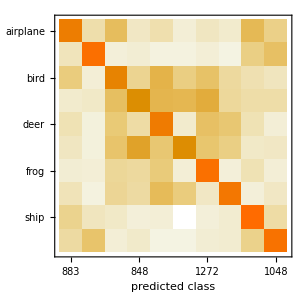
Classifier Measurements
Classifier method | Net
Number of test examples | 10000
Accuracy | (70.00.5) %
Accuracy baseline | (10.000.30) %
Geometric mean of probabilities | 0.433 ± 0.0044
Mean cross entropy | 0.838 ± 0.01
Single evaluation time | 5.98 ms/example
Batch evaluation speed | 2.14 examples/ms
-Graphics- |

```mathematica
tdNet=NetExtract[results["TrainedNet"],"MyNet"];
tdNet=NetReplacePart[tdNet,{"Input"->mnistEncoder,"Output"->cifarDecoder}];

measurements=ClassifierMeasurements[tdNet,testData]
```

```mathematica
measurements["Accuracy"]
measurements["WorstClassifiedExamples"]
```

0.6871

{-Graphics-→truck,-Graphics-→deer,-Graphics-→airplane,-Graphics-→deer,-Graphics-→cat,-Graphics-→ship,-Graphics-→airplane,-Graphics-→cat,-Graphics-→airplane,-Graphics-→truck}

```mathematica
measurements["LeastCertainExamples"]
```

{-Graphics-→automobile,-Graphics-→horse,-Graphics-→frog,-Graphics-→cat,-Graphics-→bird,-Graphics-→dog,-Graphics-→airplane,-Graphics-→deer,-Graphics-→truck,-Graphics-→automobile}

```mathematica
measurements["TopConfusions"]
```

{bird→deer,cat→frog,cat→dog,automobile→truck,cat→deer,airplane→bird,deer→frog,bird→dog,bird→frog,deer→horse}